## System Hamiltonians

Identity operator

```mathematica
Id[ve_,ho_]:=ve,ho
```

There are two subsystems A and B, each of which are two level systems

```mathematica
HASep[veA_,hoA_,veB_,hoB_]:=({{(ℏ Subscript[ω, 1])/2, 0}, {0, -(ℏ Subscript[ω, 1])/2}})[[veA,hoA]]Id[veB,hoB]
HBSep[veA_,hoA_,veB_,hoB_]:=Id[veA,hoA]({{(ℏ Subscript[ω, 2])/2, 0}, {0, -(ℏ Subscript[ω, 2])/2}})[[veB,hoB]]
```

Eigenstates,
|1>	= |e,e>
|2>	= |e,g>
|3>	= |g,e>
|4>	= |g,g>

Eigenstate mapping function, (maps overall state (1 to 4) to subsystem A, B state,

```mathematica
EmapA[i_]:=(i,3+i,4)2+(i,1+i,2)1
EmapB[i_]:=(i,2+i,4)2+(i,1+i,3)1
```

Matrix form of the two Hamiltonians

```mathematica
HA[ve_,ho_]:=HASep[EmapA[ve],EmapA[ho],EmapB[ve],EmapB[ho]]
HB[ve_,ho_]:=HBSep[EmapA[ve],EmapA[ho],EmapB[ve],EmapB[ho]]
```

System Hamiltonians in combined system matrix form

```mathematica
HAMatrix=Table[HA[ve,ho],{ve,1,4},{ho,1,4}];
MatrixForm[HAMatrix]
HBMatrix=Table[HB[ve,ho],{ve,1,4},{ho,1,4}];
MatrixForm[HBMatrix]
```

((ℏ ω_1)/2 | 0 | 0 | 0
0 | (ℏ ω_1)/2 | 0 | 0
0 | 0 | -(ℏ ω_1)/2 | 0
0 | 0 | 0 | -(ℏ ω_1)/2)

((ℏ ω_2)/2 | 0 | 0 | 0
0 | -(ℏ ω_2)/2 | 0 | 0
0 | 0 | (ℏ ω_2)/2 | 0
0 | 0 | 0 | -(ℏ ω_2)/2)

## Interaction Hamiltonian between the two TLSs

Interaction between the two systems are of the form H_int= -1/2ℏ γ(σ_+^1⊗σ_-^2+σ_-^1⊗σ_+^2) =-1/2ℏ γ (|e_1><g_1|⊗|g_2><e_2|+|g_1><e_1|⊗|e_2><g_2|)

```mathematica
Hint[ve_,ho_]:=+(ℏ γ)/2 (KroneckerProduct[({{0, 1}, {0, 0}}),({{0, 0}, {1, 0}})]+KroneckerProduct[({{0, 0}, {1, 0}}),({{0, 1}, {0, 0}})])[[ve,ho]]
```

```mathematica
HintMatrix:=Table[Hint[ve,ho],{ve,1,4},{ho,1,4}];
MatrixForm[HintMatrix]
```

(0 | 0 | 0 | 0
0 | 0 | (γ ℏ)/2 | 0
0 | (γ ℏ)/2 | 0 | 0
0 | 0 | 0 | 0)

## Combined system Hamiltonian

```mathematica
HtotMatrix=HAMatrix+HBMatrix+HintMatrix;
MatrixForm[HtotMatrix]
```

((ℏ ω_1)/2+(ℏ ω_2)/2 | 0 | 0 | 0
0 | (ℏ ω_1)/2-(ℏ ω_2)/2 | (γ ℏ)/2 | 0
0 | (γ ℏ)/2 | -(ℏ ω_1)/2+(ℏ ω_2)/2 | 0
0 | 0 | 0 | -(ℏ ω_1)/2-(ℏ ω_2)/2)

### Visualize the energy levels of the combined system

```mathematica
unitassum={ℏ->1};
```

#### Bare energy levels without the interaction Hamiltonian

```mathematica
Shift1[i_]:=i,1 4+i,2 2+i,3 3+i,4 1
```

```mathematica
HAHBEVal[i_]:=Eigenvalues[HAMatrix+HBMatrix][[Shift1[i]]]
HAHBEVec[i_]:=Eigenvectors[HAMatrix+HBMatrix][[Shift1[i]]]

Table[{HAHBEVal[i],MatrixForm[HAHBEVec[i]]},{i,1,4}]
```

{{1/2 ℏ (ω_1+ω_2),(1
0
0
0)},{1/2 ℏ (ω_1-ω_2),(0
1
0
0)},{1/2 ℏ (-ω_1+ω_2),(0
0
1
0)},{1/2 ℏ (-ω_1-ω_2),(0
0
0
1)}}

```mathematica
Manipulate[Module[{temp},
temp=Table[HAHBEVal[i],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,unitassum}];
Plot[temp,{t,0,2},PlotLegends->{"|1> = |ee>","|2> = |eg>","|3> = |ge>","|4> = |gg>"},AxesLabel->{None,"Energy"},PlotRange->{-1.5,1.5},Ticks->{None,Automatic}]
],
Delimiter,Item["Frequencies",Alignment->Center],
{{ω1,0.9},0,3},{{ω2,1.1},0,3}]
```

#### Dressed energy levels with the interaction Hamiltonian

```mathematica
Shift2[i_]:=i,1 2+i,2 4+i,3 3+i,4 1
```

```mathematica
HtotEVal[i_]:=Eigenvalues[HtotMatrix][[Shift2[i]]]
HtotEVec[i_]:=Simplify[Normalize[Eigenvectors[HtotMatrix][[Shift2[i]]]]]

Table[{HtotEVal[i],MatrixForm[HtotEVec[i]]},{i,1,4}]
```

{{1/2 ℏ (ω_1+ω_2),(1
0
0
0)},{1/2 ℏ √(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2),(0
(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2))
1/(√(1+Abs[(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2))
0)},{-1/2 ℏ √(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2),(0
-(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2))
1/(√(1+Abs[(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2))
0)},{1/2 ℏ (-ω_1-ω_2),(0
0
0
1)}}

```mathematica
Manipulate[Module[{temp},
temp=Table[HtotEVal[i],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,unitassum}];
Plot[temp,{t,0,2},PlotLegends->{"|1_DRE> = |ee>","|2_DRE>","|3_DRE>","|4_DRE> = |gg>"},AxesLabel->{None,"Energy"},PlotRange->{-1.5,1.5},Ticks->{None,Automatic}]
],
Delimiter,Item["Frequencies",Alignment->Center],
{{ω1,0.9},0,3},{{ω2,1.1},0,3},
Delimiter,Item["Interaction strength",Alignment->Center],
{{γs,0.0},0,3}]
```

Introducing the interaction Hamiltonian further separates the middle two energy levels.

#### Resonant coupling (i.e. ω_1=ω_2)

```mathematica
Manipulate[Module[{temp},
temp=Table[HtotEVal[i],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ωs,Subscript[ω, 2]->ωs,γ->γs,unitassum}];
Plot[temp,{t,0,2},PlotLegends->{"|1_DRE> = |ee>","|2_DRE>","|3_DRE>","|4_DRE> = |gg>"},AxesLabel->{None,"Energy"},PlotRange->{-1.5,1.5},Ticks->{None,Automatic}]
],
Delimiter,Item["Frequencies",Alignment->Center],
{{ωs,0.9},0,3},
Delimiter,Item["Interaction strength",Alignment->Center],
{{γs,0.0},0,3}]
```

## Representing the system Hamiltonian in new (dressed) |i_DRE>; i=1,2,3,4 basis

Bare eigensystem (without interaction)

```mathematica
Table[{HAHBEVal[i],MatrixForm[HAHBEVec[i]]},{i,1,4}]
```

{{1/2 ℏ (ω_1+ω_2),(1
0
0
0)},{1/2 ℏ (ω_1-ω_2),(0
1
0
0)},{1/2 ℏ (-ω_1+ω_2),(0
0
1
0)},{1/2 ℏ (-ω_1-ω_2),(0
0
0
1)}}

Define 
	Detuning  Δ= (ω_1-ω_2)
	Rabi frequency Ω = √(γ^2+Δ^2)

Dressed eigensystem (with interaction)

```mathematica
Table[{HtotEVal[i],MatrixForm[HtotEVec[i]]},{i,1,4}]//.{√(γ^2+Subscript[ω, 1]^2-2 Subscript[ω, 1] Subscript[ω, 2]+Subscript[ω, 2]^2)->Ω,-Subscript[ω, 1]+Subscript[ω, 2]->-Δ,Subscript[ω, 1]-Subscript[ω, 2]->Δ}
```

{{1/2 ℏ (ω_1+ω_2),(1
0
0
0)},{(Ω ℏ)/2,(0
(Δ+Ω)/(γ √(1+Abs[(Δ+Ω)/γ]^2))
1/(√(1+Abs[(Δ+Ω)/γ]^2))
0)},{-(Ω ℏ)/2,(0
-(-Δ+Ω)/(γ √(1+Abs[(-Δ+Ω)/γ]^2))
1/(√(1+Abs[(-Δ+Ω)/γ]^2))
0)},{1/2 ℏ (-ω_1-ω_2),(0
0
0
1)}}

Simplifying,

```mathematica
({{0}, {(Δ+Ω)/(γ √(1+Abs[(Δ+Ω)/γ]^2))}, {1/(√(1+Abs[(Δ+Ω)/γ]^2))}, {0}})=({{0}, {(Δ+Ω)/(√(γ^2+(Δ+Ω)^2))}, {γ/(√(γ^2+(Δ+Ω)^2))}, {0}})=1/(√(γ^2+(Ω+Δ)^2))({{0}, {Δ+Ω}, {γ}, {0}})
({{0}, {-(-Δ+Ω)/(γ √(1+Abs[(-Δ+Ω)/γ]^2))}, {1/(√(1+Abs[(-Δ+Ω)/γ]^2))}, {0}})=({{0}, {-(Ω-Δ)/(√(γ^2+(Ω-Δ)^2))}, {γ/(√(γ^2+(Ω-Δ)^2))}, {0}})=1/(√(γ^2+(Ω-Δ)^2))({{0}, {Δ-Ω}, {γ}, {0}})
```

```mathematica
HtotEValSimp[i_]:={1/2 ℏ (Subscript[ω, 1]+Subscript[ω, 2]),1/2 ℏ Ω,-1/2 ℏ Ω,-1/2 ℏ (Subscript[ω, 1]+Subscript[ω, 2])}[[i]]
HtotEVecSimp[i_]:={({{1}, {0}, {0}, {0}}),1/(√(γ^2+(Ω+Δ)^2))({{0}, {(Ω+Δ)}, {γ}, {0}}),1/(√(γ^2+(Ω-Δ)^2))({{0}, {Δ-Ω}, {γ}, {0}}),({{0}, {0}, {0}, {1}})}[[i]]
```

Diagonalizing the new Hamiltonian on |1_DRE>, |2_DRE>, |3_DRE> and |4_DRE> given above can bring it back to a form without the interaction Hamiltonian but with different ω_1 and ω_2.
	ω_1^INT=ω_1-Ω/2
	ω_2^INT=ω_2+Ω/2
Have to be careful because two middle eigenvectors are now mixed states.

### Diagonalizing the system Hamiltonian (in the dressed system basis)

Make a matrix out of the unit eigenvectors

```mathematica
HtotEVecMatrix=Table[HtotEVec[i],{i,1,4}];
```

Verify the diagonalization relation

```mathematica
HtotMatrix//MatrixForm
Simplify[(Inverse[HtotEVecMatrix].DiagonalMatrix[Table[HtotEVal[i],{i,1,4}]].HtotEVecMatrix)]//MatrixForm
```

((ℏ ω_1)/2+(ℏ ω_2)/2 | 0 | 0 | 0
0 | (ℏ ω_1)/2-(ℏ ω_2)/2 | (γ ℏ)/2 | 0
0 | (γ ℏ)/2 | -(ℏ ω_1)/2+(ℏ ω_2)/2 | 0
0 | 0 | 0 | -(ℏ ω_1)/2-(ℏ ω_2)/2)

(1/2 ℏ (ω_1+ω_2) | 0 | 0 | 0
0 | 1/2 ℏ (ω_1-ω_2) | (γ ℏ)/2 | 0
0 | (γ ℏ)/2 | -1/2 ℏ (ω_1-ω_2) | 0
0 | 0 | 0 | -1/2 ℏ (ω_1+ω_2))

The diagonalization is through a unitary transformation with U being the eigenvector matrix.

Inverting the unitary transformation gives the Hamiltonian in the |1_INT>, |2_INT>, |3_INT> and |4_INT> basis,

```mathematica
HtotDREMatrix=Simplify[HtotEVecMatrix.HtotMatrix.Inverse[HtotEVecMatrix]];
MatrixForm[HtotDREMatrix]
```

(1/2 ℏ (ω_1+ω_2) | 0 | 0 | 0
0 | 1/2 ℏ √(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2) | 0 | 0
0 | 0 | -1/2 ℏ √(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2) | 0
0 | 0 | 0 | -1/2 ℏ (ω_1+ω_2))

Substituting for Ω to simplify the formula,

```mathematica
HtotDRESimpMatrix=({{1/2 ℏ (Subscript[ω, 1]+Subscript[ω, 2]), 0, 0, 0}, {0, 1/2 ℏ Ω, 0, 0}, {0, 0, -1/2 ℏ Ω, 0}, {0, 0, 0, -1/2 ℏ (Subscript[ω, 1]+Subscript[ω, 2])}});
```

```mathematica
HtotEVecSimpMatrix=Table[HtotEVecSimp[i],{i,1,4}];
```

Verify both eigenvector matrices are physically the same thing

```mathematica
HtotEVecMatrix//MatrixForm
HtotEVecSimpMatrix//MatrixForm
```

(1 | 0 | 0 | 0
0 | (ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2)) | 1/(√(1+Abs[(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2)) | 0
0 | -(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2)) | 1/(√(1+Abs[(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2)) | 0
0 | 0 | 0 | 1)

(1 | 0 | 0 | 0
0 | (Δ+Ω)/(√(γ^2+(Δ+Ω)^2)) | γ/(√(γ^2+(Δ+Ω)^2)) | 0
0 | (Δ-Ω)/(√(γ^2+(-Δ+Ω)^2)) | γ/(√(γ^2+(-Δ+Ω)^2)) | 0
0 | 0 | 0 | 1)

We will work in this basis from now on,
	with the Hamiltonian

```mathematica
HtotDRESimpMatrix//MatrixForm
```

(1/2 ℏ (ω_1+ω_2) | 0 | 0 | 0
0 | (Ω ℏ)/2 | 0 | 0
0 | 0 | -(Ω ℏ)/2 | 0
0 | 0 | 0 | -1/2 ℏ (ω_1+ω_2))

and eigensystem

```mathematica
Shift3[i_]:=i,1 4+i,2 2+i,3 1+i,4 3
```

```mathematica
HtotDRESSimpEVal[i_]:=Eigenvalues[HtotDRESimpMatrix][[Shift3[i]]]
HtotDRESSimpEVec[i_]:=Simplify[Normalize[Eigenvectors[HtotDRESimpMatrix][[Shift3[i]]]]]

Table[{HtotDRESSimpEVal[i],MatrixForm[HtotDRESSimpEVec[i]]},{i,1,4}]
```

{{1/2 ℏ (ω_1+ω_2),(1
0
0
0)},{(Ω ℏ)/2,(0
1
0
0)},{-(Ω ℏ)/2,(0
0
1
0)},{1/2 ℏ (-ω_1-ω_2),(0
0
0
1)}}

## Density Matrix

```mathematica
ρDREMatrix[t_]:=Table[Subscript[ρ, ve,ho][t],{ve,1,4},{ho,1,4}]
```

```mathematica
MatrixForm[ρDREMatrix[t]]
```

(ρ_(1,1)[t] | ρ_(1,2)[t] | ρ_(1,3)[t] | ρ_(1,4)[t]
ρ_(2,1)[t] | ρ_(2,2)[t] | ρ_(2,3)[t] | ρ_(2,4)[t]
ρ_(3,1)[t] | ρ_(3,2)[t] | ρ_(3,3)[t] | ρ_(3,4)[t]
ρ_(4,1)[t] | ρ_(4,2)[t] | ρ_(4,3)[t] | ρ_(4,4)[t])

## Pauli matrices

### In z-base representation

|+z>=(1,0)
|-z>=(0,1)

```mathematica
Subscript[σ, axis_][ve_,ho_]:=axis,1({{0, 1}, {1, 0}})[[ve,ho]]+axis,2({{0, -ⅈ}, {ⅈ, 0}})[[ve,ho]]+axis,3({{1, 0}, {0, -1}})[[ve,ho]];
Id[ve_,ho_]:=ve,ho
```

```mathematica
{Table[Subscript[σ, 1][ve,ho],{ve,1,2},{ho,1,2}],Table[Subscript[σ, 2][ve,ho],{ve,1,2},{ho,1,2}],Table[Subscript[σ, 3][ve,ho],{ve,1,2},{ho,1,2}]};
Map[MatrixForm,%,1]
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

### In compound system representation

```mathematica
Subscript[σ, P_,axis_][ve_,ho_]:=
P,1(Subscript[σ, axis][EmapA[ve],EmapA[ho]]Id[EmapB[ve],EmapB[ho]])+
P,2(Id[EmapA[ve],EmapA[ho]]Subscript[σ, axis][EmapB[ve],EmapB[ho]])

Subscript[σMatrix, P_,axis_]:=Table[Subscript[σ, P,axis][ve,ho],{ve,1,4},{ho,1,4}]
Subscript[σPMatrix, P_]:=1/2(Subscript[σMatrix, P,1]+ⅈ Subscript[σMatrix, P,2])
Subscript[σMMatrix, P_]:=1/2(Subscript[σMatrix, P,1]-ⅈ Subscript[σMatrix, P,2])
```

```mathematica
{MatrixForm[Subscript[σMatrix, 1,1]],MatrixForm[Subscript[σMatrix, 2,1]]}
{MatrixForm[Subscript[σMatrix, 1,2]],MatrixForm[Subscript[σMatrix, 2,2]]}
{MatrixForm[Subscript[σMatrix, 1,3]],MatrixForm[Subscript[σMatrix, 2,3]]}
{MatrixForm[Subscript[σPMatrix, 1]],MatrixForm[Subscript[σPMatrix, 2]]}
{MatrixForm[Subscript[σMMatrix, 1]],MatrixForm[Subscript[σMMatrix, 2]]}
```

{(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)}

{(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0)}

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)}

{(0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0)}

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0)}

### In new |i_DRE> dressed system basis

We put the Pauli matrices through the same unitary transformation we used above to convert HtotMatrix to HtotINTMatrix

```mathematica
Subscript[σDREMatrix, P_,axis_]:=HtotEVecSimpMatrix.Subscript[σMatrix, P,axis].Inverse[HtotEVecSimpMatrix]
Subscript[σPDREMatrix, P_]:=HtotEVecSimpMatrix.Subscript[σPMatrix, P].Inverse[HtotEVecSimpMatrix]
Subscript[σMDREMatrix, P_]:=HtotEVecSimpMatrix.Subscript[σMMatrix, P].Inverse[HtotEVecSimpMatrix]
```

```mathematica
{MatrixForm[Subscript[σDREMatrix, 1,1]],MatrixForm[Subscript[σDREMatrix, 2,1]]}
```

{(0 | ((-Δ+Ω) √(γ^2+(Δ+Ω)^2))/(2 γ Ω) | -((-Δ-Ω) √(γ^2+(-Δ+Ω)^2))/(2 γ Ω) | 0
γ/(√(γ^2+(Δ+Ω)^2)) | 0 | 0 | (-Δ-Ω)/(√(γ^2+(Δ+Ω)^2))
γ/(√(γ^2+(-Δ+Ω)^2)) | 0 | 0 | (-Δ+Ω)/(√(γ^2+(-Δ+Ω)^2))
0 | -(√(γ^2+(Δ+Ω)^2))/(2 Ω) | (√(γ^2+(-Δ+Ω)^2))/(2 Ω) | 0),(0 | -(√(γ^2+(Δ+Ω)^2))/(2 Ω) | (√(γ^2+(-Δ+Ω)^2))/(2 Ω) | 0
(-Δ-Ω)/(√(γ^2+(Δ+Ω)^2)) | 0 | 0 | γ/(√(γ^2+(Δ+Ω)^2))
(-Δ+Ω)/(√(γ^2+(-Δ+Ω)^2)) | 0 | 0 | γ/(√(γ^2+(-Δ+Ω)^2))
0 | ((-Δ+Ω) √(γ^2+(Δ+Ω)^2))/(2 γ Ω) | -((-Δ-Ω) √(γ^2+(-Δ+Ω)^2))/(2 γ Ω) | 0)}

## Thermal interactions with the environment

Each of the two TLSs interact thermally with respective thermal baths B_A and B_B with temperatures T_A and T_B.

Interaction Hamiltonian between the thermal bath L or R with the two TLSs

```mathematica
Subscript[H, TLS-bath]^P=ℏ Subscript[σ, X]^P∑_k Subscript[g, k](Subscript[a, k]^P+Subscript[a, k]^P†)
```

To get the Lindbladian operators, we use equation (15) of Optically Controlled Quantum Thermal Gate paper.

### Get projection matrices Π(ϵ)

```mathematica
πMatrix[i_]:={({{1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}),({{0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}),({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}}),({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}})}[[i]]
```

### Enumerate all possible transitions

Dummy ω values

```mathematica
ωassum={Subscript[ω, 1]==10,Subscript[ω, 2]==9,Ω==2};
```

Transition frequencies,

```mathematica
ω[m_,n_]:=Simplify[(HtotDRESSimpEVal[m]-HtotDRESSimpEVal[n])/ℏ]
```

Unique and positive transition frequencies,

```mathematica
ω[i_]:=Module[{temp1,temp2,temp3},
temp1=Flatten[Table[ω[m,n],{m,1,4},{n,m+1,4}]];
temp2=Simplify[temp1,Assumptions->ωassum];
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
DeleteCases[temp1 temp3,0][[i]]
]
ωsize:=Module[{temp1,temp2,temp3},
temp1=Flatten[Table[ω[m,n],{m,1,4},{n,m+1,4}]];
temp2=Simplify[temp1,Assumptions->ωassum];
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
Dimensions[DeleteCases[temp1 temp3,0]][[1]]
]
```

List all transition frequencies

```mathematica
Table[ω[i],{i,1,ωsize}]
ωsize
```

{1/2 (-Ω+ω_1+ω_2),1/2 (Ω+ω_1+ω_2),ω_1+ω_2,Ω}

4

### Get Lindblad operators A^P(ω)

```mathematica
Subscript[AMatrix, P_][ωs_]:=Simplify[∑_(i=1)^ωsize ∑_(j=1)^ωsize ωs,ω[i,j]πMatrix[j].Subscript[σDREMatrix, P,1].πMatrix[i],Assumptions->{Ω>0,Subscript[ω, 1]>0,Subscript[ω, 2]>0,Subscript[ω, 1]+Subscript[ω, 2]>3Ω}]
```

Lindbladian terms involve a summation of A^P(ω) terms for positive omega.

```mathematica
Table[MatrixForm[Subscript[AMatrix, 1][ω[i]]],{i,1,ωsize}]
Table[MatrixForm[Subscript[AMatrix, 2][ω[i]]],{i,1,ωsize}]
```

{(0 | 0 | 0 | 0
γ/(√(γ^2+(Δ+Ω)^2)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -(√(γ^2+(Δ-Ω)^2))/(2 Ω) | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
γ/(√(γ^2+(Δ-Ω)^2)) | 0 | 0 | 0
0 | (√(γ^2+(Δ+Ω)^2))/(2 Ω) | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

{(0 | 0 | 0 | 0
(Δ+Ω)/(√(γ^2+(Δ+Ω)^2)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | (√(γ^2+(Δ-Ω)^2) (Δ+Ω))/(2 γ Ω) | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
(Δ-Ω)/(√(γ^2+(Δ-Ω)^2)) | 0 | 0 | 0
0 | ((-Δ+Ω) √(γ^2+(Δ+Ω)^2))/(2 γ Ω) | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

Linbladian for the Markovian quantum master equation,

```mathematica
Subscript[LinMatrix, P_][ρ_]:=J[Subscript[ω, P]](1+Subscript[NBE, P][Subscript[ω, P]])(Subscript[AMatrix, P][Subscript[ω, P]].ρ.Subscript[AMatrix, P][Subscript[ω, P]]†-1/2(Subscript[AMatrix, P][Subscript[ω, P]]†.Subscript[AMatrix, P][Subscript[ω, P]].ρ+ρ.Subscript[AMatrix, P][Subscript[ω, P]]†.Subscript[AMatrix, P][Subscript[ω, P]]))+J[Subscript[ω, P]]Subscript[NBE, P][Subscript[ω, P]](Subscript[AMatrix, P][Subscript[ω, P]]†.ρ.Subscript[AMatrix, P][Subscript[ω, P]]-1/2(Subscript[AMatrix, P][Subscript[ω, P]].Subscript[AMatrix, P][Subscript[ω, P]]†.ρ+ρ.Subscript[AMatrix, P][Subscript[ω, P]].Subscript[AMatrix, P][Subscript[ω, P]]†))
```

Net thermal decaying rate Τ_P[i,j] from state | i > to state | j > while releasing energy to reservoir P. Note i > j.
Τs_P[i,j] is used due to variable naming issues.

```mathematica
Subscript[Τs, P_][i_,j_]:=J[Subscript[ω, P]](1+Subscript[NBE, P][Subscript[ω, P]])Subscript[ρ, {i,i}][t]-J[Subscript[ω, P]]Subscript[NBE, P][Subscript[ω, P]]Subscript[ρ, {j,j}][t]
```

Internal L-R interaction induced transition rate Υ[i,j] from state | i > to state | j > while transferring energy within the system.
Υs[i,j] is used due to variable naming issues.

```mathematica
Υs[i_,j_]:= γ/2 ⅈ(Subscript[ρ, {i,j}][t]-Subscript[ρ, {j,i}][t])
```

Mathematica function for arithmetically proper replacements,

```mathematica
ReplaceArithmetically[expr_,orig_,repl_]:=
Module[{f},
(*Actual replacement function, but it is not Listable*)
f[exprs_,origs_,repls_]:=Module[{q,r},
{q,r}=PolynomialReduce[exprs,origs,{}];
q.repls+r
];
(*Construct for making the function Listable in only the first argument*)
Function[t,f[t,orig,repl],{Listable}][expr]
]
```

```mathematica
ReplaceArithmetically[Subscript[LinMatrix, 1][ρMatrix[t]],
{Subscript[Τs, 1][1,3],Subscript[Τs, 1][2,4]},
{Subscript[Τ, 1][1,3],Subscript[Τ, 1][2,4]}
];
MatrixForm[%]

ReplaceArithmetically[Subscript[LinMatrix, 2][ρMatrix[t]],
{Subscript[Τs, 2][1,2],Subscript[Τs, 2][3,4]},
{Subscript[Τ, 2][1,2],Subscript[Τ, 2][3,4]}
];
MatrixForm[%]
```

(-Τ_1[1,3] | -J[ω_1] ρ_{1,2}[t]+J[ω_1] NBE_1[ω_1] (-ρ_{1,2}[t]+ρ_{3,4}[t]) | 1/2 (-J[ω_1] ρ_{1,3}[t]-2 J[ω_1] NBE_1[ω_1] ρ_{1,3}[t]) | 1/2 (-J[ω_1] ρ_{1,4}[t]-2 J[ω_1] NBE_1[ω_1] ρ_{1,4}[t])
-J[ω_1] ρ_{2,1}[t]+J[ω_1] NBE_1[ω_1] (-ρ_{2,1}[t]+ρ_{4,3}[t]) | -Τ_1[2,4] | 1/2 (-J[ω_1] ρ_{2,3}[t]-2 J[ω_1] NBE_1[ω_1] ρ_{2,3}[t]) | 1/2 (-J[ω_1] ρ_{2,4}[t]-2 J[ω_1] NBE_1[ω_1] ρ_{2,4}[t])
1/2 (-J[ω_1] ρ_{3,1}[t]-2 J[ω_1] NBE_1[ω_1] ρ_{3,1}[t]) | 1/2 (-J[ω_1] ρ_{3,2}[t]-2 J[ω_1] NBE_1[ω_1] ρ_{3,2}[t]) | Τ_1[1,3] | J[ω_1] ρ_{1,2}[t]+J[ω_1] NBE_1[ω_1] (ρ_{1,2}[t]-ρ_{3,4}[t])
1/2 (-J[ω_1] ρ_{4,1}[t]-2 J[ω_1] NBE_1[ω_1] ρ_{4,1}[t]) | 1/2 (-J[ω_1] ρ_{4,2}[t]-2 J[ω_1] NBE_1[ω_1] ρ_{4,2}[t]) | J[ω_1] ρ_{2,1}[t]+J[ω_1] NBE_1[ω_1] (ρ_{2,1}[t]-ρ_{4,3}[t]) | Τ_1[2,4])

(-Τ_2[1,2] | 1/2 (-J[ω_2] ρ_{1,2}[t]-2 J[ω_2] NBE_2[ω_2] ρ_{1,2}[t]) | -J[ω_2] ρ_{1,3}[t]+J[ω_2] NBE_2[ω_2] (-ρ_{1,3}[t]+ρ_{2,4}[t]) | 1/2 (-J[ω_2] ρ_{1,4}[t]-2 J[ω_2] NBE_2[ω_2] ρ_{1,4}[t])
1/2 (-J[ω_2] ρ_{2,1}[t]-2 J[ω_2] NBE_2[ω_2] ρ_{2,1}[t]) | Τ_2[1,2] | 1/2 (-J[ω_2] ρ_{2,3}[t]-2 J[ω_2] NBE_2[ω_2] ρ_{2,3}[t]) | J[ω_2] ρ_{1,3}[t]+J[ω_2] NBE_2[ω_2] (ρ_{1,3}[t]-ρ_{2,4}[t])
-J[ω_2] ρ_{3,1}[t]+J[ω_2] NBE_2[ω_2] (-ρ_{3,1}[t]+ρ_{4,2}[t]) | 1/2 (-J[ω_2] ρ_{3,2}[t]-2 J[ω_2] NBE_2[ω_2] ρ_{3,2}[t]) | -Τ_2[3,4] | 1/2 (-J[ω_2] ρ_{3,4}[t]-2 J[ω_2] NBE_2[ω_2] ρ_{3,4}[t])
1/2 (-J[ω_2] ρ_{4,1}[t]-2 J[ω_2] NBE_2[ω_2] ρ_{4,1}[t]) | J[ω_2] ρ_{3,1}[t]+J[ω_2] NBE_2[ω_2] (ρ_{3,1}[t]-ρ_{4,2}[t]) | 1/2 (-J[ω_2] ρ_{4,3}[t]-2 J[ω_2] NBE_2[ω_2] ρ_{4,3}[t]) | Τ_2[3,4])

## Quantum Markovian master equation

Ohmic bath spectral density,

```mathematica
Jassum=J[ω_]->κ ω;
```

Right hand side of the Markovian quantum master equation (in Schrodinger picture),

```mathematica
RHS=-ⅈ/ℏ(HtotMatrix.ρMatrix[t]-ρMatrix[t].HtotMatrix)+Subscript[LinMatrix, 1][ρMatrix[t]]+Subscript[LinMatrix, 2][ρMatrix[t]];
MatrixForm[%]
```

(-J[ω_1] (1+NBE_1[ω_1]) ρ_{1,1}[t]-J[ω_2] (1+NBE_2[ω_2]) ρ_{1,1}[t]+J[ω_2] NBE_2[ω_2] ρ_{2,2}[t]+J[ω_1] NBE_1[ω_1] ρ_{3,3}[t] | -J[ω_1] (1+NBE_1[ω_1]) ρ_{1,2}[t]-1/2 J[ω_2] NBE_2[ω_2] ρ_{1,2}[t]-1/2 J[ω_2] (1+NBE_2[ω_2]) ρ_{1,2}[t]-(ⅈ (-((ℏ ω_1)/2-(ℏ ω_2)/2) ρ_{1,2}[t]+((ℏ ω_1)/2+(ℏ ω_2)/2) ρ_{1,2}[t]+1/2 γ ℏ ρ_{1,3}[t]))/ℏ+J[ω_1] NBE_1[ω_1] ρ_{3,4}[t] | -1/2 J[ω_1] NBE_1[ω_1] ρ_{1,3}[t]-1/2 J[ω_1] (1+NBE_1[ω_1]) ρ_{1,3}[t]-J[ω_2] (1+NBE_2[ω_2]) ρ_{1,3}[t]-(ⅈ (1/2 γ ℏ ρ_{1,2}[t]-(-(ℏ ω_1)/2+(ℏ ω_2)/2) ρ_{1,3}[t]+((ℏ ω_1)/2+(ℏ ω_2)/2) ρ_{1,3}[t]))/ℏ+J[ω_2] NBE_2[ω_2] ρ_{2,4}[t] | -1/2 J[ω_1] NBE_1[ω_1] ρ_{1,4}[t]-1/2 J[ω_1] (1+NBE_1[ω_1]) ρ_{1,4}[t]-1/2 J[ω_2] NBE_2[ω_2] ρ_{1,4}[t]-1/2 J[ω_2] (1+NBE_2[ω_2]) ρ_{1,4}[t]-(ⅈ (-(-(ℏ ω_1)/2-(ℏ ω_2)/2) ρ_{1,4}[t]+((ℏ ω_1)/2+(ℏ ω_2)/2) ρ_{1,4}[t]))/ℏ
-J[ω_1] (1+NBE_1[ω_1]) ρ_{2,1}[t]-1/2 J[ω_2] NBE_2[ω_2] ρ_{2,1}[t]-1/2 J[ω_2] (1+NBE_2[ω_2]) ρ_{2,1}[t]-(ⅈ (((ℏ ω_1)/2-(ℏ ω_2)/2) ρ_{2,1}[t]-((ℏ ω_1)/2+(ℏ ω_2)/2) ρ_{2,1}[t]-1/2 γ ℏ ρ_{3,1}[t]))/ℏ+J[ω_1] NBE_1[ω_1] ρ_{4,3}[t] | J[ω_2] (1+NBE_2[ω_2]) ρ_{1,1}[t]-J[ω_1] (1+NBE_1[ω_1]) ρ_{2,2}[t]-J[ω_2] NBE_2[ω_2] ρ_{2,2}[t]-(ⅈ (1/2 γ ℏ ρ_{2,3}[t]-1/2 γ ℏ ρ_{3,2}[t]))/ℏ+J[ω_1] NBE_1[ω_1] ρ_{4,4}[t] | -1/2 J[ω_1] NBE_1[ω_1] ρ_{2,3}[t]-1/2 J[ω_1] (1+NBE_1[ω_1]) ρ_{2,3}[t]-1/2 J[ω_2] NBE_2[ω_2] ρ_{2,3}[t]-1/2 J[ω_2] (1+NBE_2[ω_2]) ρ_{2,3}[t]-(ⅈ (1/2 γ ℏ ρ_{2,2}[t]+((ℏ ω_1)/2-(ℏ ω_2)/2) ρ_{2,3}[t]-(-(ℏ ω_1)/2+(ℏ ω_2)/2) ρ_{2,3}[t]-1/2 γ ℏ ρ_{3,3}[t]))/ℏ | J[ω_2] (1+NBE_2[ω_2]) ρ_{1,3}[t]-1/2 J[ω_1] NBE_1[ω_1] ρ_{2,4}[t]-1/2 J[ω_1] (1+NBE_1[ω_1]) ρ_{2,4}[t]-J[ω_2] NBE_2[ω_2] ρ_{2,4}[t]-(ⅈ (-(-(ℏ ω_1)/2-(ℏ ω_2)/2) ρ_{2,4}[t]+((ℏ ω_1)/2-(ℏ ω_2)/2) ρ_{2,4}[t]-1/2 γ ℏ ρ_{3,4}[t]))/ℏ
-1/2 J[ω_1] NBE_1[ω_1] ρ_{3,1}[t]-1/2 J[ω_1] (1+NBE_1[ω_1]) ρ_{3,1}[t]-J[ω_2] (1+NBE_2[ω_2]) ρ_{3,1}[t]-(ⅈ (-1/2 γ ℏ ρ_{2,1}[t]+(-(ℏ ω_1)/2+(ℏ ω_2)/2) ρ_{3,1}[t]-((ℏ ω_1)/2+(ℏ ω_2)/2) ρ_{3,1}[t]))/ℏ+J[ω_2] NBE_2[ω_2] ρ_{4,2}[t] | -1/2 J[ω_1] NBE_1[ω_1] ρ_{3,2}[t]-1/2 J[ω_1] (1+NBE_1[ω_1]) ρ_{3,2}[t]-1/2 J[ω_2] NBE_2[ω_2] ρ_{3,2}[t]-1/2 J[ω_2] (1+NBE_2[ω_2]) ρ_{3,2}[t]-(ⅈ (-1/2 γ ℏ ρ_{2,2}[t]-((ℏ ω_1)/2-(ℏ ω_2)/2) ρ_{3,2}[t]+(-(ℏ ω_1)/2+(ℏ ω_2)/2) ρ_{3,2}[t]+1/2 γ ℏ ρ_{3,3}[t]))/ℏ | J[ω_1] (1+NBE_1[ω_1]) ρ_{1,1}[t]-(ⅈ (-1/2 γ ℏ ρ_{2,3}[t]+1/2 γ ℏ ρ_{3,2}[t]))/ℏ-J[ω_1] NBE_1[ω_1] ρ_{3,3}[t]-J[ω_2] (1+NBE_2[ω_2]) ρ_{3,3}[t]+J[ω_2] NBE_2[ω_2] ρ_{4,4}[t] | J[ω_1] (1+NBE_1[ω_1]) ρ_{1,2}[t]-J[ω_1] NBE_1[ω_1] ρ_{3,4}[t]-1/2 J[ω_2] NBE_2[ω_2] ρ_{3,4}[t]-1/2 J[ω_2] (1+NBE_2[ω_2]) ρ_{3,4}[t]-(ⅈ (-1/2 γ ℏ ρ_{2,4}[t]-(-(ℏ ω_1)/2-(ℏ ω_2)/2) ρ_{3,4}[t]+(-(ℏ ω_1)/2+(ℏ ω_2)/2) ρ_{3,4}[t]))/ℏ
-1/2 J[ω_1] NBE_1[ω_1] ρ_{4,1}[t]-1/2 J[ω_1] (1+NBE_1[ω_1]) ρ_{4,1}[t]-1/2 J[ω_2] NBE_2[ω_2] ρ_{4,1}[t]-1/2 J[ω_2] (1+NBE_2[ω_2]) ρ_{4,1}[t]-(ⅈ ((-(ℏ ω_1)/2-(ℏ ω_2)/2) ρ_{4,1}[t]-((ℏ ω_1)/2+(ℏ ω_2)/2) ρ_{4,1}[t]))/ℏ | J[ω_2] (1+NBE_2[ω_2]) ρ_{3,1}[t]-1/2 J[ω_1] NBE_1[ω_1] ρ_{4,2}[t]-1/2 J[ω_1] (1+NBE_1[ω_1]) ρ_{4,2}[t]-J[ω_2] NBE_2[ω_2] ρ_{4,2}[t]-(ⅈ ((-(ℏ ω_1)/2-(ℏ ω_2)/2) ρ_{4,2}[t]-((ℏ ω_1)/2-(ℏ ω_2)/2) ρ_{4,2}[t]+1/2 γ ℏ ρ_{4,3}[t]))/ℏ | J[ω_1] (1+NBE_1[ω_1]) ρ_{2,1}[t]-J[ω_1] NBE_1[ω_1] ρ_{4,3}[t]-1/2 J[ω_2] NBE_2[ω_2] ρ_{4,3}[t]-1/2 J[ω_2] (1+NBE_2[ω_2]) ρ_{4,3}[t]-(ⅈ (1/2 γ ℏ ρ_{4,2}[t]+(-(ℏ ω_1)/2-(ℏ ω_2)/2) ρ_{4,3}[t]-(-(ℏ ω_1)/2+(ℏ ω_2)/2) ρ_{4,3}[t]))/ℏ | J[ω_1] (1+NBE_1[ω_1]) ρ_{2,2}[t]+J[ω_2] (1+NBE_2[ω_2]) ρ_{3,3}[t]-J[ω_1] NBE_1[ω_1] ρ_{4,4}[t]-J[ω_2] NBE_2[ω_2] ρ_{4,4}[t])

```mathematica
ReplaceArithmetically[RHS,
{Subscript[Τs, 1][1,3],Subscript[Τs, 2][1,2],Subscript[Τs, 2][3,4],Subscript[Τs, 1][2,4],Υs[2,3]},
{Subscript[Τ, 1][1,3],Subscript[Τ, 2][1,2],Subscript[Τ, 2][3,4],Subscript[Τ, 1][2,4],Υ[2,3]}
];
MatrixForm[%]
```

(-Τ_1[1,3]-Τ_2[1,2] | -1/2 ⅈ (-2 ⅈ J[ω_1] ρ_{1,2}[t]-ⅈ J[ω_2] ρ_{1,2}[t]+2 ω_2 ρ_{1,2}[t]-2 ⅈ J[ω_1] NBE_1[ω_1] ρ_{1,2}[t]-2 ⅈ J[ω_2] NBE_2[ω_2] ρ_{1,2}[t]+γ ρ_{1,3}[t]+2 ⅈ J[ω_1] NBE_1[ω_1] ρ_{3,4}[t]) | -1/2 ⅈ (γ ρ_{1,2}[t]-ⅈ J[ω_1] ρ_{1,3}[t]-2 ⅈ J[ω_2] ρ_{1,3}[t]+2 ω_1 ρ_{1,3}[t]-2 ⅈ J[ω_1] NBE_1[ω_1] ρ_{1,3}[t]-2 ⅈ J[ω_2] NBE_2[ω_2] ρ_{1,3}[t]+2 ⅈ J[ω_2] NBE_2[ω_2] ρ_{2,4}[t]) | 1/2 (-J[ω_1] ρ_{1,4}[t]-J[ω_2] ρ_{1,4}[t]-2 ⅈ ω_1 ρ_{1,4}[t]-2 ⅈ ω_2 ρ_{1,4}[t]-2 J[ω_1] NBE_1[ω_1] ρ_{1,4}[t]-2 J[ω_2] NBE_2[ω_2] ρ_{1,4}[t])
1/2 ⅈ (2 ⅈ J[ω_1] ρ_{2,1}[t]+ⅈ J[ω_2] ρ_{2,1}[t]+2 ω_2 ρ_{2,1}[t]+2 ⅈ J[ω_1] NBE_1[ω_1] ρ_{2,1}[t]+2 ⅈ J[ω_2] NBE_2[ω_2] ρ_{2,1}[t]+γ ρ_{3,1}[t]-2 ⅈ J[ω_1] NBE_1[ω_1] ρ_{4,3}[t]) | -Υ[2,3]-Τ_1[2,4]+Τ_2[1,2] | -1/2 ⅈ (γ ρ_{2,2}[t]-ⅈ J[ω_1] ρ_{2,3}[t]-ⅈ J[ω_2] ρ_{2,3}[t]+2 ω_1 ρ_{2,3}[t]-2 ω_2 ρ_{2,3}[t]-2 ⅈ J[ω_1] NBE_1[ω_1] ρ_{2,3}[t]-2 ⅈ J[ω_2] NBE_2[ω_2] ρ_{2,3}[t]-γ ρ_{3,3}[t]) | 1/2 ⅈ (-2 ⅈ J[ω_2] ρ_{1,3}[t]-2 ⅈ J[ω_2] NBE_2[ω_2] ρ_{1,3}[t]+ⅈ J[ω_1] ρ_{2,4}[t]-2 ω_1 ρ_{2,4}[t]+2 ⅈ J[ω_1] NBE_1[ω_1] ρ_{2,4}[t]+2 ⅈ J[ω_2] NBE_2[ω_2] ρ_{2,4}[t]+γ ρ_{3,4}[t])
1/2 ⅈ (γ ρ_{2,1}[t]+ⅈ J[ω_1] ρ_{3,1}[t]+2 ⅈ J[ω_2] ρ_{3,1}[t]+2 ω_1 ρ_{3,1}[t]+2 ⅈ J[ω_1] NBE_1[ω_1] ρ_{3,1}[t]+2 ⅈ J[ω_2] NBE_2[ω_2] ρ_{3,1}[t]-2 ⅈ J[ω_2] NBE_2[ω_2] ρ_{4,2}[t]) | 1/2 ⅈ (γ ρ_{2,2}[t]+ⅈ J[ω_1] ρ_{3,2}[t]+ⅈ J[ω_2] ρ_{3,2}[t]+2 ω_1 ρ_{3,2}[t]-2 ω_2 ρ_{3,2}[t]+2 ⅈ J[ω_1] NBE_1[ω_1] ρ_{3,2}[t]+2 ⅈ J[ω_2] NBE_2[ω_2] ρ_{3,2}[t]-γ ρ_{3,3}[t]) | Υ[2,3]+Τ_1[1,3]-Τ_2[3,4] | 1/2 ⅈ (-2 ⅈ J[ω_1] ρ_{1,2}[t]-2 ⅈ J[ω_1] NBE_1[ω_1] ρ_{1,2}[t]+γ ρ_{2,4}[t]+ⅈ J[ω_2] ρ_{3,4}[t]-2 ω_2 ρ_{3,4}[t]+2 ⅈ J[ω_1] NBE_1[ω_1] ρ_{3,4}[t]+2 ⅈ J[ω_2] NBE_2[ω_2] ρ_{3,4}[t])
1/2 (-J[ω_1] ρ_{4,1}[t]-J[ω_2] ρ_{4,1}[t]+2 ⅈ ω_1 ρ_{4,1}[t]+2 ⅈ ω_2 ρ_{4,1}[t]-2 J[ω_1] NBE_1[ω_1] ρ_{4,1}[t]-2 J[ω_2] NBE_2[ω_2] ρ_{4,1}[t]) | -1/2 ⅈ (2 ⅈ J[ω_2] ρ_{3,1}[t]+2 ⅈ J[ω_2] NBE_2[ω_2] ρ_{3,1}[t]-ⅈ J[ω_1] ρ_{4,2}[t]-2 ω_1 ρ_{4,2}[t]-2 ⅈ J[ω_1] NBE_1[ω_1] ρ_{4,2}[t]-2 ⅈ J[ω_2] NBE_2[ω_2] ρ_{4,2}[t]+γ ρ_{4,3}[t]) | -1/2 ⅈ (2 ⅈ J[ω_1] ρ_{2,1}[t]+2 ⅈ J[ω_1] NBE_1[ω_1] ρ_{2,1}[t]+γ ρ_{4,2}[t]-ⅈ J[ω_2] ρ_{4,3}[t]-2 ω_2 ρ_{4,3}[t]-2 ⅈ J[ω_1] NBE_1[ω_1] ρ_{4,3}[t]-2 ⅈ J[ω_2] NBE_2[ω_2] ρ_{4,3}[t]) | Τ_1[2,4]+Τ_2[3,4])

Left hand side of the Markovian quantum master equation,

```mathematica
LHS=D[ρMatrix[t], t];
MatrixForm[%]
```

(ρ_{1,1}'[t] | ρ_{1,2}'[t] | ρ_{1,3}'[t] | ρ_{1,4}'[t]
ρ_{2,1}'[t] | ρ_{2,2}'[t] | ρ_{2,3}'[t] | ρ_{2,4}'[t]
ρ_{3,1}'[t] | ρ_{3,2}'[t] | ρ_{3,3}'[t] | ρ_{3,4}'[t]
ρ_{4,1}'[t] | ρ_{4,2}'[t] | ρ_{4,3}'[t] | ρ_{4,4}'[t])

Markovian quantum master equation for a general density matrix,

```mathematica
sol=Flatten[Solve[LHS==RHS,Flatten[Table[Subscript[ρ, {i,j}]'[t],{i,1,4},{j,1,4}]]]/.Rule->Equal];
```

```mathematica
{J[Subscript[ω, 1]],J[Subscript[ω, 2]]};
Flatten[Table[Subscript[ρ, {i,j}][t],{i,1,4},{j,1,4}]];
sol=ApplySides[Collect[Expand[#],%%,Collect[#,%]&]&,sol]
```

{ρ_{1,1}'[t]==J[ω_2] ((-1-NBE_2[ω_2]) ρ_{1,1}[t]+NBE_2[ω_2] ρ_{2,2}[t])+J[ω_1] ((-1-NBE_1[ω_1]) ρ_{1,1}[t]+NBE_1[ω_1] ρ_{3,3}[t]),ρ_{1,2}'[t]==-ⅈ ω_2 ρ_{1,2}[t]+J[ω_2] (-1/2-NBE_2[ω_2]) ρ_{1,2}[t]-1/2 ⅈ γ ρ_{1,3}[t]+J[ω_1] ((-1-NBE_1[ω_1]) ρ_{1,2}[t]+NBE_1[ω_1] ρ_{3,4}[t]),ρ_{1,3}'[t]==-1/2 ⅈ γ ρ_{1,2}[t]-ⅈ ω_1 ρ_{1,3}[t]+J[ω_1] (-1/2-NBE_1[ω_1]) ρ_{1,3}[t]+J[ω_2] ((-1-NBE_2[ω_2]) ρ_{1,3}[t]+NBE_2[ω_2] ρ_{2,4}[t]),ρ_{1,4}'[t]==(-ⅈ ω_1-ⅈ ω_2) ρ_{1,4}[t]+J[ω_1] (-1/2-NBE_1[ω_1]) ρ_{1,4}[t]+J[ω_2] (-1/2-NBE_2[ω_2]) ρ_{1,4}[t],ρ_{2,1}'[t]==ⅈ ω_2 ρ_{2,1}[t]+J[ω_2] (-1/2-NBE_2[ω_2]) ρ_{2,1}[t]+1/2 ⅈ γ ρ_{3,1}[t]+J[ω_1] ((-1-NBE_1[ω_1]) ρ_{2,1}[t]+NBE_1[ω_1] ρ_{4,3}[t]),ρ_{2,2}'[t]==J[ω_2] ((1+NBE_2[ω_2]) ρ_{1,1}[t]-NBE_2[ω_2] ρ_{2,2}[t])-1/2 ⅈ γ ρ_{2,3}[t]+1/2 ⅈ γ ρ_{3,2}[t]+J[ω_1] ((-1-NBE_1[ω_1]) ρ_{2,2}[t]+NBE_1[ω_1] ρ_{4,4}[t]),ρ_{2,3}'[t]==-1/2 ⅈ γ ρ_{2,2}[t]+(-ⅈ ω_1+ⅈ ω_2) ρ_{2,3}[t]+J[ω_1] (-1/2-NBE_1[ω_1]) ρ_{2,3}[t]+J[ω_2] (-1/2-NBE_2[ω_2]) ρ_{2,3}[t]+1/2 ⅈ γ ρ_{3,3}[t],ρ_{2,4}'[t]==-ⅈ ω_1 ρ_{2,4}[t]+J[ω_1] (-1/2-NBE_1[ω_1]) ρ_{2,4}[t]+J[ω_2] ((1+NBE_2[ω_2]) ρ_{1,3}[t]-NBE_2[ω_2] ρ_{2,4}[t])+1/2 ⅈ γ ρ_{3,4}[t],ρ_{3,1}'[t]==1/2 ⅈ γ ρ_{2,1}[t]+ⅈ ω_1 ρ_{3,1}[t]+J[ω_1] (-1/2-NBE_1[ω_1]) ρ_{3,1}[t]+J[ω_2] ((-1-NBE_2[ω_2]) ρ_{3,1}[t]+NBE_2[ω_2] ρ_{4,2}[t]),ρ_{3,2}'[t]==1/2 ⅈ γ ρ_{2,2}[t]+(ⅈ ω_1-ⅈ ω_2) ρ_{3,2}[t]+J[ω_1] (-1/2-NBE_1[ω_1]) ρ_{3,2}[t]+J[ω_2] (-1/2-NBE_2[ω_2]) ρ_{3,2}[t]-1/2 ⅈ γ ρ_{3,3}[t],ρ_{3,3}'[t]==1/2 ⅈ γ ρ_{2,3}[t]-1/2 ⅈ γ ρ_{3,2}[t]+J[ω_1] ((1+NBE_1[ω_1]) ρ_{1,1}[t]-NBE_1[ω_1] ρ_{3,3}[t])+J[ω_2] ((-1-NBE_2[ω_2]) ρ_{3,3}[t]+NBE_2[ω_2] ρ_{4,4}[t]),ρ_{3,4}'[t]==1/2 ⅈ γ ρ_{2,4}[t]-ⅈ ω_2 ρ_{3,4}[t]+J[ω_2] (-1/2-NBE_2[ω_2]) ρ_{3,4}[t]+J[ω_1] ((1+NBE_1[ω_1]) ρ_{1,2}[t]-NBE_1[ω_1] ρ_{3,4}[t]),ρ_{4,1}'[t]==(ⅈ ω_1+ⅈ ω_2) ρ_{4,1}[t]+J[ω_1] (-1/2-NBE_1[ω_1]) ρ_{4,1}[t]+J[ω_2] (-1/2-NBE_2[ω_2]) ρ_{4,1}[t],ρ_{4,2}'[t]==ⅈ ω_1 ρ_{4,2}[t]+J[ω_1] (-1/2-NBE_1[ω_1]) ρ_{4,2}[t]+J[ω_2] ((1+NBE_2[ω_2]) ρ_{3,1}[t]-NBE_2[ω_2] ρ_{4,2}[t])-1/2 ⅈ γ ρ_{4,3}[t],ρ_{4,3}'[t]==-1/2 ⅈ γ ρ_{4,2}[t]+ⅈ ω_2 ρ_{4,3}[t]+J[ω_2] (-1/2-NBE_2[ω_2]) ρ_{4,3}[t]+J[ω_1] ((1+NBE_1[ω_1]) ρ_{2,1}[t]-NBE_1[ω_1] ρ_{4,3}[t]),ρ_{4,4}'[t]==J[ω_1] ((1+NBE_1[ω_1]) ρ_{2,2}[t]-NBE_1[ω_1] ρ_{4,4}[t])+J[ω_2] ((1+NBE_2[ω_2]) ρ_{3,3}[t]-NBE_2[ω_2] ρ_{4,4}[t])}

Separate diagonal and off diagonal equations,

```mathematica
soldiag=sol[[1;; ;;5]];
soloffdiag=Delete[sol,Table[{1+5i},{i,0,3}]];
```

Diagonals of the Markovian quantum master equation simplified to transition rates,

```mathematica
soldiagtran=ApplySides[
ReplaceArithmetically[Simplify[#],
{Subscript[Τs, 1][1,3],Subscript[Τs, 2][1,2],Subscript[Τs, 2][3,4],Subscript[Τs, 1][2,4],Υs[2,3]},
{Subscript[Τ, 1][1,3],Subscript[Τ, 2][1,2],Subscript[Τ, 2][3,4],Subscript[Τ, 1][2,4],Υ[2,3]}
]&,soldiag]
```

{ρ_{1,1}'[t]==-Τ_1[1,3]-Τ_2[1,2],ρ_{2,2}'[t]==-Υ[2,3]-Τ_1[2,4]+Τ_2[1,2],ρ_{3,3}'[t]==Υ[2,3]+Τ_1[1,3]-Τ_2[3,4],ρ_{4,4}'[t]==Τ_1[2,4]+Τ_2[3,4]}

## Dynamical heat flows

Thermal distributions in the environments (Bose Einstein distribution),

```mathematica
NBEassum=Subscript[NBE, P_][ω_]-> 1/(ⅇ^(ω Subscript[β, P])-1);
```

```mathematica
NBEassum=Subscript[NBE, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, P]))-1);
```

```mathematica
Manipulate[Plot[{Subscript[NBE, 1][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 1]->T1},Subscript[NBE, 2][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 2]->T2}},{ω,0,10 0.2},PlotRange-> {0,2},PlotLegends->{"L","R"},AxesLabel->{"ω","P[ω]"}]
,{{T1,0.2},0.01,1},{{T2,0.1},0.01,1}]
```

ReplaceRepeated::reps: {NBEassum,k→1,ℏ→1,T_1→0.2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {NBEassum,k→1.,ℏ→1.,T_1→0.2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {NBEassum,k→1,ℏ→1,T_1→0.2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

```mathematica
Manipulate[Plot[{Subscript[NBE, 1][ω]//.{NBEassum,k-> 1.38 10^-23,ℏ->1.054 10^-34,Subscript[T, 1]->T1},Subscript[NBE, 2][ω]//.{NBEassum,k-> 1.38 10^-23,ℏ->1.054 10^-34,Subscript[T, 2]->T2}},{ω,0,10 k/ℏ 300/.{k-> 1.3806 10^-23,ℏ->1.0546 10^-34}},PlotRange-> {0,2},PlotLegends->{"L","R"},AxesLabel->{"ω","P[ω]"}]
,{{T1,300},0.01,500},{{T2,150},0.01,500}]
```

ReplaceRepeated::reps: {NBEassum,k→1.38×10^-23,ℏ→1.054×10^-34,T_1→300} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {NBEassum,k→1.38×10^-23,ℏ→1.054×10^-34,T_1→300.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {NBEassum,k→1.38×10^-23,ℏ→1.054×10^-34,T_1→300} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

Calculate heat current flow,

```mathematica
Subscript[EngyFlowIn, P_][ρ_]:=Tr[Subscript[LinMatrix, P][ρ].HtotMatrix]
```

```mathematica
ReplaceArithmetically[Subscript[EngyFlowIn, 1][ρMatrix[t]],
{Subscript[Τs, 1][1,3],Subscript[Τs, 2][1,2],Subscript[Τs, 2][3,4],Subscript[Τs, 1][2,4]},
{Subscript[Τ, 1][1,3],Subscript[Τ, 2][1,2],Subscript[Τ, 2][3,4],Subscript[Τ, 1][2,4]}
];
Simplify[%]

ReplaceArithmetically[Subscript[EngyFlowIn, 2][ρMatrix[t]],
{Subscript[Τs, 1][1,3],Subscript[Τs, 2][1,2],Subscript[Τs, 2][3,4],Subscript[Τs, 1][2,4]},
{Subscript[Τ, 1][1,3],Subscript[Τ, 2][1,2],Subscript[Τ, 2][3,4],Subscript[Τ, 1][2,4]}
];
Simplify[%]
```

1/4 ℏ (γ J[ω_1] (1+2 NBE_1[ω_1]) (ρ_{2,3}[t]+ρ_{3,2}[t])-4 ω_1 (Τ_1[1,3]+Τ_1[2,4]))

1/4 ℏ (γ J[ω_2] (1+2 NBE_2[ω_2]) (ρ_{2,3}[t]+ρ_{3,2}[t])-4 ω_2 (Τ_2[1,2]+Τ_2[3,4]))

## On unit conversions

To resolve the natural units to SI units, we use the relationship,
Energy = ℏ ω = k_B T
In the natural units case, we have chosen Ts to be an order of magnitude lower than the largest ωs.

In SI units, T'_H = 400, in natural units, T_H=0.2.
This gives a ratio of T'_H/T_H=2000.

Temperature conversion, T'=2000 T

Frequency conversion,  ω'=(2000 k_B)/ℏ ω, Ω'=(2000 k_B)/ℏ Ω

Time conversion,  t'=ℏ/(2000 k_B)t

Transition rates conversion, Τ'=(2000 k_B)/ℏ Τ

Energy flows conversion, J'=ℏ(2000 k_B)/ℏ(2000 k_B)/ℏ J=(2000 k_B)^2/ℏ J

Unit conversion factors for natural units,

```mathematica
unitassum = {k-> 1,ℏ->1};
```

```mathematica
Tconv=1;
ωconv=1;
tconv=1;
Τconv=1;
Econv=1;
```

Unit conversion factors for SI units,

```mathematica
unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
```

```mathematica
Tconv=300/0.2;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
```

Note - When using SI units, due to frequencies and energies being in widely different orders of magnitudes, there may be numerical errors in calculations (Removing Quiet functions in code will allow warnings about this issue to be displayed). Hence it is always advisable to confirm simulation results with natural unit simulations.

## Density matrix, transition rate and energy flow evolution with time

Assumptions on the temperatures of the baths, TLS energy levels, and TLS interaction strengths,

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[ω, 1]->1 ωconv,Subscript[ω, 2]->1 ωconv,κ-> 1 };
```

Assumption on the strength of the L-R interaction

```mathematica
γassum={γ->0.0 ωconv};
```

```mathematica
γassum={γ->0.3ωconv};
```

```mathematica
γassum={γ->1ωconv};
```

System energy matrix under above assumptions,

```mathematica
MatrixForm[HtotMatrix//.Flatten[{Tassum,unitassum,γassum}]]
```

(2.0709×10^-20 | 0 | 0 | 0
0 | 0. | -1.03545×10^-20 | 0
0 | -1.03545×10^-20 | 0. | 0
0 | 0 | 0 | -2.0709×10^-20)

Numerical solution of the dynamics, with the initial condition that all density matrix elements except the first are zero.

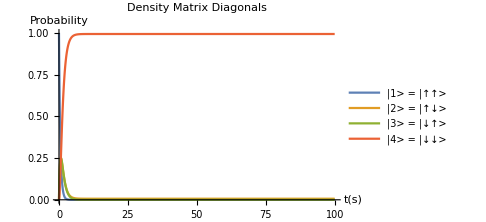

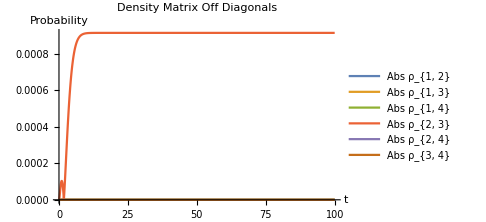

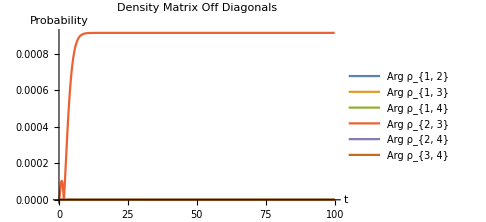

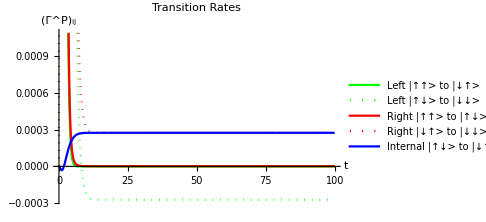

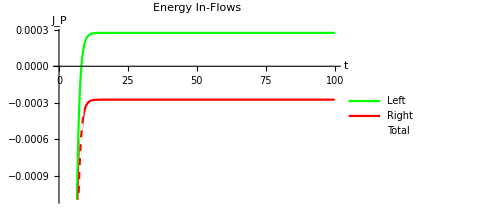

```mathematica
tmax=(100/Subscript[ω, 1])//.Flatten[{unitassum,Tassum}];

dynamics=NDSolve[
Flatten[{sol//.Flatten[{Jassum,NBEassum,Tassum,unitassum,γassum}],Table[Subscript[ρ, {i,j}][0]==i,j i,1 1,{i,1,4},{j,1,4}]}]
,Flatten[Table[Subscript[ρ, {i,j}],{i,1,4},{j,1,4}]],{t,0,tmax}
];

Flatten[{Table[Subscript[ρ, {i,i}][t],{i,1,4}]}/.dynamics];
Plot[%,{t,0,tmax},PlotRange-> {0.0,1},ImageSize->Medium,PlotLabel->  Style["Density Matrix Diagonals"],AxesLabel->{Style["t(s)"],Style["Probability"]}, 
PlotLegends->{
Style["|1> = |↑↑> "],
Style["|2> = |↑↓> "],
Style["|3> = |↓↑> "],
Style["|4> = |↓↓> "]}]

Flatten[{Abs[Subscript[ρ, {1,2}][t]],Abs[Subscript[ρ, {1,3}][t]],Abs[Subscript[ρ, {1,4}][t]],Abs[Subscript[ρ, {2,3}][t]],Arg[Subscript[ρ, {2,4}][t]],Arg[Subscript[ρ, {3,4}][t]]}/.dynamics];
Plot[%,{t,0,tmax},ImageSize->Medium,PlotLabel-> Style["Density Matrix Off Diagonals"],AxesLabel->{"t","Probability"}, PlotLegends->{"Abs ρ_{1, 2}","Abs ρ_{1, 3}","Abs ρ_{1, 4}","Abs ρ_{2, 3}","Abs ρ_{2, 4}","Abs ρ_{3, 4}"}]

Flatten[{Abs[Subscript[ρ, {1,2}][t]],Abs[Subscript[ρ, {1,3}][t]],Abs[Subscript[ρ, {1,4}][t]],Abs[Subscript[ρ, {2,3}][t]],Arg[Subscript[ρ, {2,4}][t]],Arg[Subscript[ρ, {3,4}][t]]}/.dynamics];
Plot[%,{t,0,tmax},ImageSize->Medium,PlotLabel-> Style["Density Matrix Off Diagonals"],AxesLabel->{"t","Probability"}, PlotLegends->{"Arg ρ_{1, 2}","Arg ρ_{1, 3}","Arg ρ_{1, 4}","Arg ρ_{2, 3}","Arg ρ_{2, 4}","Arg ρ_{3, 4}"}]

Flatten[
{Subscript[Τs, 1][1,3],Subscript[Τs, 1][2,4],
Subscript[Τs, 2][1,2],Subscript[Τs, 2][3,4],
Υs[2,3]
}//.Flatten[{Jassum,NBEassum,Tassum,unitassum,γassum}]
/.dynamics];
Plot[%,{t,0,tmax},PlotRange-> Automatic,ImageSize->Medium,PlotLabel-> Style["Transition Rates"],AxesLabel->{"t","(Γ^P)_ij"}, PlotLegends->{
"Left |↑↑> to |↓↑>","Left |↑↓> to |↓↓>",
"Right |↑↑> to |↑↓>","Right |↓↑> to |↓↓>","Internal |↑↓> to |↓↑>"},PlotStyle->{{Green},{Green,Dotted},{Red},{Red,Dotted},{Blue}}]

Flatten[{Subscript[EngyFlowIn, 1][ρMatrix[t]],Subscript[EngyFlowIn, 2][ρMatrix[t]],Subscript[EngyFlowIn, 1][ρMatrix[t]]+Subscript[EngyFlowIn, 2][ρMatrix[t]]}//.Flatten[{Jassum,NBEassum,Tassum,unitassum,γassum}]/.dynamics];
Plot[%,{t,0,tmax},AxesLabel->{"t","J_P"},ImageSize->Medium,PlotLabel-> Style["Energy In-Flows"],PlotLegends->{"Left ","Right","Total"},PlotStyle->{Green,Red,{White,Dashed}}]
```

## Density matrix, transition rate and energy flow at equilibrium

Function for density matrix elements, transition rates and energy flows,

```mathematica
varFunc[T1_,T2_,ω1_,ω2_,γs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{unitassum,Jassum,NBEassum,κ->1,Subscript[T, 1]->T1,Subscript[T, 2]->T2,Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs}];
temp1=N[sol//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, {i_,j_}]'[t]-> 0,Subscript[ρ, {i_,j_}][t]-> Subscript[ρ, {i,j}]},1==∑_(i=1)^4 Subscript[ρ, {i,i}]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, {i,j}],{i,1,4},{j,1,4}]]]]];

Re[{
Table[Subscript[ρ, {i,i}],{i,1,4}]/.temp3,
{Subscript[Τs, 1][1,3],Subscript[Τs, 1][2,4],Subscript[Τs, 2][1,2],Subscript[Τs, 2][3,4],Υs[2,3]}//.Flatten[{Subscript[ρ, {i_,j_}][t]->Subscript[ρ, {i,j}],temp0}]/.temp3,
{Subscript[EngyFlowIn, 1][ρMatrix[t]],Subscript[EngyFlowIn, 2][ρMatrix[t]]}//.Flatten[{Subscript[ρ, {i_,j_}][t]->Subscript[ρ, {i,j}],temp0}]/.temp3
}]
]
```

Function for drawing a state flow diagram,

```mathematica
DrawFlowGraph[label_,posx_,posy_,nodes_,rates_,ratecolors_,ratesF_,ratecolorsF_,title_,maxrate_]:=Module[{pos,psize},
psize=Dimensions[label][[1]];
pos[i_]:={posx[[i]],posy[[i]]};
Graphics[Flatten[{
{Thickness[0.0001],Arrowheads[0.03],Black,Arrow[{{1.15Min[posx],1.2Min[posy]},{1.15Min[posx],1.1Max[posy]}}]},Black,{Text[Style["Energy",FontSize->13.6,FontFamily->"Times New Roman"],{1.0Min[posx]-0.03,1.15Max[posy]}],Text[Style[title,FontSize->13.6,FontFamily->"Times New Roman"],{-0.2,1.27Min[posy]}]},

Table[{Opacity[1],Thick,RGBColor[0.08,0.56,1],Disk[pos[i],0.01+0.22 √nodes[[i]]]},{i,1,psize}],
Table[
	If[rates[[i,j]]≠0 ,
		If[ ratesF[[i,j]]≠0,
			If[Abs[rates[[i,j]]]>Abs[ratesF[[i,j]]],
				{Opacity[0.8],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
				ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]],
				Opacity[1],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
				ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
			,
				{Opacity[0.8],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
				ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]],
				Opacity[1],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
				ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
			]
		,
			{Opacity[0.8],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
			ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
		]
	,
		If[ ratesF[[i,j]]≠0,
			{Opacity[0.8],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
			ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
		, Nothing]
	]
,{i,1,psize-1},{j,i+1,psize}],
Table[{Opacity[1],Black,Text[Style[label[[i]],FontSize->12],{posx[[i]]+{0,0.04,0,0.06,0.04,0,0.04,0}[[i]],posy[[i]]+{0.045,0.08,-0.05,-0.06,0.06,-0.05,-0.08,0.045}[[i]]}]},{i,1,psize}]

}], ImageSize->Medium]
]

DrawFunc[T1_,T2_,ω1_,ω2_,title_,maxrate_,var_]:=Module[{label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF,temp0},temp0=Flatten[{Jassum,NBEassum,k->1,κ->1,Subscript[T, 1]-> T1,Subscript[T, 2]-> T2,Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2}];label={"|↑↑>","|↑↓>","|↓↑>","|↓↓>"};posx={0,-0.4,0.4,0};posy=Diagonal[HtotMatrix/(ℏ ωconv)/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2}]];nodes=var[[1]];rates=({{0, var[[2]][[3]], var[[2]][[1]], 0}, {0, 0, 0, var[[2]][[2]]}, {0, 0, 0, var[[2]][[4]]}, {0, 0, 0, 0}});
ratesF=({{0, 0, 0, 0}, {0, 0, var[[2]][[5]], 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});ratecolors=({{0, Red, Green, 0}, {0, 0, 0, Green}, {0, 0, 0, Red}, {0, 0, 0, 0}});
ratecolorsF=({{0, 0, 0, 0}, {0, 0, Blue, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
DrawFlowGraph[label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF,title,maxrate]
]
```

Steady-state energy flows, transition rates, density matrix diagonals and energy eigenvalues, plotted for dynamically changeable bath, and system parameters,

```mathematica
Manipulate[Module[{temp},
temp=varFunc[T1,T2,ω1,ω2,γs,unitassum];
{
DrawFunc[T1,T2,ω1,ω2,StringForm["γ=``",γs],Τmax,temp],

BarChart[temp[[3]]
,ChartLabels->{"Left ","Right"},PlotLabel->"Equilibrium energy inflow",AxesLabel->{"","J_P(J)"},ImageSize->Medium,PlotRange->{-Emax,Emax},ChartStyle->{Green,Red}],

BarChart[temp[[2]]
,ChartLabels->Placed[{"L |↑↑> to |↓↑>","L |↑↓> to |↓↓>","R |↑↑> to |↑↓>","R |↓↑> to |↓↓>","F |↑↓> to |↓↑>"},Center,Rotate[#,π/2]&],PlotLabel->"Equilibrium thermal transition rate",ImageSize->Medium,ChartStyle->{Green,Green,Red,Red,Blue}],

BarChart[temp[[1]]
,ChartLabels->{"ρ_{1, 1}","ρ_{2, 2}","ρ_{3, 3}","ρ_{4, 4}"},PlotLabel->"Equilibrium density matrix",ImageSize->Medium,PlotRange->{-0.1,1},ChartStyle->"Pastel"]
}],
{{T1,0.20 Tconv},0.001 Tconv,1 Tconv},
{{T2,0.02 Tconv},0.001 Tconv,1 Tconv},
{{ω1,0.6ωconv},0ωconv,2ωconv},
{{ω2,1.4ωconv},0ωconv,2ωconv},
{{γs,1ωconv},0ωconv,5ωconv},
{{Emax,0.01Econv},0.00001Econv,0.01Econv},
{{Τmax,0.08Τconv},0.0001Τconv,0.2Τconv}]
```

BarChart::ldata: 0.895 is not a valid dataset or list of datasets.

BarChart::ldata: 0.02 is not a valid dataset or list of datasets.

BarChart::ldata: 0.2 is not a valid dataset or list of datasets.

General::stop: Further output of BarChart::ldata will be suppressed during this calculation.